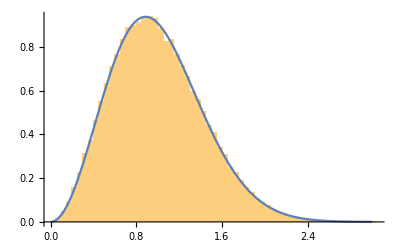

```mathematica
Clear["Global`*"]
(*2×2的随机厄密复矩阵*)
n = 100000;
eglist = Table[Eigenvalues[RandomVariate[GaussianUnitaryMatrixDistribution[2]]],{i,1,n}];
egspace = Table[Differences[Sort[eglist[[i]]]],{i,1,n}]//Flatten;
norms = egspace/Mean[egspace];
p[x_]:=32/Pi^2×x^2 Exp[-4/Pi×x^2];
Show[{Histogram[norms,{0.05},"PDF"],Plot[p[x],{x,0,3}]}]
```

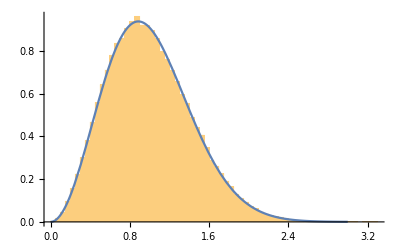

```mathematica
Clear["Global`*"]
(*3×3的随机厄密复矩阵*)
n = 100000;
eglist = Table[Eigenvalues[RandomVariate[GaussianUnitaryMatrixDistribution[3]]],{i,1,n}];
egspace = Table[Differences[Sort[eglist[[i]]]],{i,1,n}]//Flatten;
norms = egspace/Mean[egspace];
p[x_]:=32/Pi^2×x^2 Exp[-4/Pi×x^2];
Show[{Histogram[norms,{0.05},"PDF"],Plot[p[x],{x,0,3}]}]
```

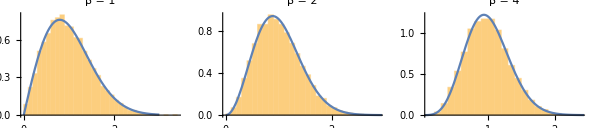

```mathematica
Clear["Global`*"]
(*不同分布下的结果*)
gaussiandists={GaussianOrthogonalMatrixDistribution[2],GaussianUnitaryMatrixDistribution[2],GaussianSymplecticMatrixDistribution[2]};
spacingdists=MatrixPropertyDistribution[{-1,1}.MinMax[Eigenvalues[x]],x\[Distributed]#]&/@gaussiandists;
gaps=Normalize[RandomVariate[#,10000],Mean]&/@spacingdists;
WignerSurmisePDF[x_,β:1]:=Pi (x/2) Exp[-Pi (x/2)^2]
WignerSurmisePDF[x_,β:2]:=2 (4 x/Pi)^2 Exp[(-4/Pi) x^2]
WignerSurmisePDF[x_,β:4]:=(64/(9 Pi))^3 x^4 Exp[(-64/(9 Pi)) x^2]
histogram=Histogram[#,{0.1},PDF]&/@gaps;
plot=Plot[WignerSurmisePDF[x,#],{x,0,3}]&/@{1,2,4};
GraphicsRow@MapThread[Show[#1,#2,ImageSize->180,PlotLabel->Row[{"β = ",#3}]]&,{histogram,plot,{1,2,4}}]
```